## Solutions: Mathematica 6 Lab 6

Problem 1: River Meanders

```mathematica
α=π/5;
a=Sin[α];
b=Cos[α];
```

```mathematica
x1[θ_]:=a+Cos[θ]
x2[θ_]:=3a+Cos[θ]
x3[θ_]:=5a+Cos[θ]
x4[θ_]:=7a+Cos[θ]
x5[θ_]:=9a+Cos[θ]
y[θ_]:=b+Sin[θ]
z[θ_]:=-b+Sin[θ]
```

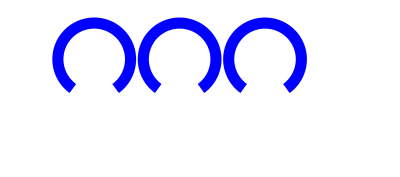

```mathematica
upperloops=ParametricPlot[{{x1[θ],y[θ]},{x3[θ],y[θ]},{x5[θ],y[θ]}},{θ,-π/2+α,(3π)/2-α},
AspectRatio->Automatic,
PlotStyle->{
{Blue,Thickness[0.02]},
{Blue,Thickness[0.02]},
{Blue,Thickness[0.02]}},Axes->False,PlotRange->{{-1,8},{-2,2}}]
```

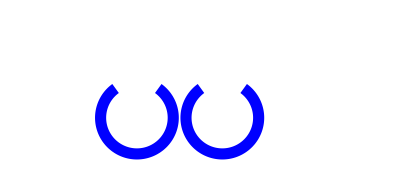

```mathematica
lowerloops=ParametricPlot[{{x2[θ],z[θ]},{x4[θ],z[θ]}},{θ,-(3π)/2+α,π/2-α},
AspectRatio->Automatic,
PlotStyle->{
{Blue,Thickness[0.02]},
{Blue,Thickness[0.02]}},Axes->False,PlotRange->{{-1,8},{-2,2}}]
```

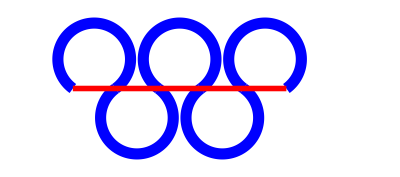

```mathematica
Show[upperloops,lowerloops,Graphics[{Thickness[0.01],Red,Line[{{0,0},{10a,0}}]}]]
```

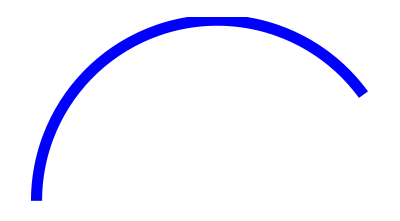

```mathematica
bluearc=ParametricPlot[{Cos[θ],Sin[θ]},{θ,α,π},AspectRatio->Automatic,
Ticks->False,Axes->False,PlotStyle->{Blue,
Thickness[0.02]}]
```

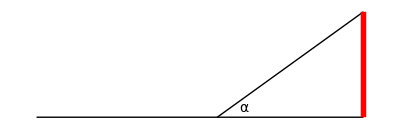

```mathematica
lines=Graphics[{Line[{{-1,0},{Cos[α],0}}],
Line[{{0,0},{Cos[α],Sin[α]}}],
{Red,Thickness[0.01],
Line[{{Cos[α],0},{Cos[α],Sin[α]}}]},Text[StyleForm["α",FontSize->14],{0.15,0.05}]}]
```

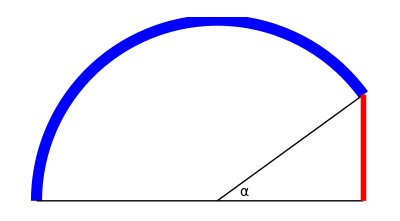

```mathematica
Show[bluearc,lines]
```

```mathematica
Clear[α]
```

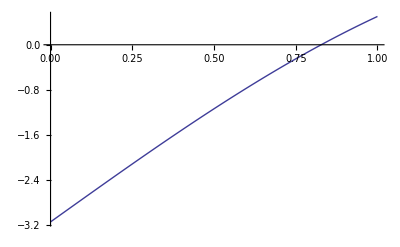

```mathematica
Plot[π Sin[α]+α-π,{α,0,1}]
```

```mathematica
α/.FindRoot[π Sin[α]+α-π==0,{α,0.8}]
```

0.827859

```mathematica
%180/π
```

47.4328

```mathematica
α=0.827858
a=Sin[α]
b=Cos[α]
```

0.827858

0.736484

0.676455

```mathematica
x1[θ_]:=a+Cos[θ]
x2[θ_]:=3a+Cos[θ]
x3[θ_]:=5a+Cos[θ]
x4[θ_]:=7a+Cos[θ]
x5[θ_]:=9a+Cos[θ]
y[θ_]:=b+Sin[θ]
z[θ_]:=-b+Sin[θ]
```

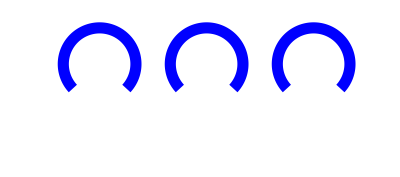

```mathematica
upperloops=ParametricPlot[{{x1[θ],y[θ]},{x3[θ],y[θ]},{x5[θ],y[θ]}},{θ,-π/2+α,(3π)/2-α},
AspectRatio->Automatic,
PlotStyle->{
{Blue,Thickness[0.02]},
{Blue,Thickness[0.02]},
{Blue,Thickness[0.02]}},Axes->False,PlotRange->{{-1,8},{-2,2}}]
```

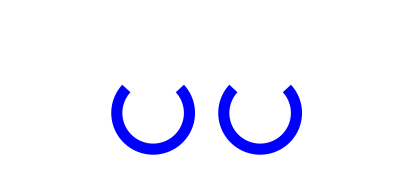

```mathematica
lowerloops=ParametricPlot[{{x2[θ],z[θ]},{x4[θ],z[θ]}},{θ,-(3π)/2+α,π/2-α},
AspectRatio->Automatic,
PlotStyle->{
{Blue,Thickness[0.02]},
{Blue,Thickness[0.02]}},Axes->False,PlotRange->{{-1,8},{-2,2}}]
```

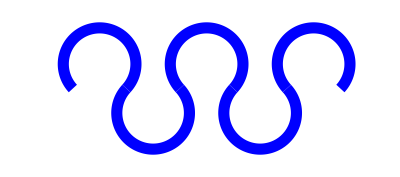

```mathematica
Show[upperloops,lowerloops]
```

Problem 2: Solitons

```mathematica
Clear[a,b]
```

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n. 
D[f,x,y,…] differentiates f successively with respect to x,y,….
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…).

```mathematica
u[x_,t_,b_]:=b^2 2 Sech[b  x-4 b^3 t]^2
```

```mathematica
D[u[x,t,b],t]+6u[x,t,b]D[u[x,t,b],x]+ D[u[x,t,b],{x,3}]==0
```

-16 b^5 Sech[4 b^3 t-b x]^2 Tanh[4 b^3 t-b x]+48 b^5 Sech[4 b^3 t-b x]^4 Tanh[4 b^3 t-b x]+2 b^2 (-16 b^3 Sech[4 b^3 t-b x]^4 Tanh[4 b^3 t-b x]+8 b^3 Sech[4 b^3 t-b x]^2 Tanh[4 b^3 t-b x]^3)==0

```mathematica
Simplify[%]
```

True

```mathematica
Animate[Plot[{u[x,t,1],u[x,t,1/(√2)]},{x,-4,20},PlotRange->{0,3}],{t,0,4},AnimationRunning->False]
```

Problem 3: Fourier Analysis of Gaussian & Soliton

```mathematica
Clear[a,b,g]
```

```mathematica
?FourierTransform
?InverseFourierTransform
```

FourierTransform[expr,t,ω] gives the symbolic Fourier transform of expr. 
FourierTransform[expr,{t_1,t_2,…},{ω_1,ω_2,…}] gives the multidimensional Fourier transform of expr.

RowBox[{"InverseFourierTransform", "[", RowBox[{StyleBox["expr", "TI"], ",", "ω", ",", StyleBox["t", "TI"]}], "]"}] gives the symbolic inverse Fourier transform of StyleBox["expr", "TI"]. 
RowBox[{"InverseFourierTransform", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox["ω", StyleBox["1", "TR"]], ",", SubscriptBox["ω", StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives the multidimensional inverse Fourier transform of StyleBox["expr", "TI"].

```mathematica
g[x_,a_]:=√(a/(2π))ⅇ^(-1/2 a x^2)
```

```mathematica
∫_(-∞)^∞ g[x,a]ⅆx
```

1/(√(2 π))√a If[Re[a]>0,(√(2 π))/(√a),Integrate[ⅇ^(-(a x^2)/2),{x,-∞,∞},Assumptions→Re[a]≤0]]

```mathematica
G[y_,a_]:=FourierTransform[g[x,a],x,y]
```

```mathematica
g[x,a]
G[y,a]
```

(√a ⅇ^(-(a x^2)/2))/(√(2 π))

(ⅇ^(-y^2/(2 a)))/(√(2 π))

```mathematica
Manipulate[GraphicsGrid[{{Plot[Evaluate[g[x,a]],{x,-5,5},PlotStyle->{Red,Thick}, PlotRange->{0,1.0},AxesLabel->{x,"Gaussian"}]},{Plot[Evaluate[G[y,a]],{y,-5,5},PlotStyle->{Blue,Thick}, PlotRange->{0,1.0},AxesLabel->{y,"Its Fourier Transform"}]}}],{a,1/5,5}]
```

```mathematica
g[x,a]==InverseFourierTransform[G[y,a],y,x]
```

True

```mathematica
h[x_,b_]:=b/2 Sech[b x]^2
```

```mathematica
∫_(-∞)^∞ h[x,b]ⅆx
```

1/2 b If[Re[b]>0,2/b,Integrate[Sech[b x]^2,{x,-∞,∞},Assumptions→Re[b]≤0]]

```mathematica
H[y_,b_]:=FourierTransform[b/2 Sech[b x]^2,x,y]
```

```mathematica
H[y,b]
```

(√(π/2) y Csch[(π y)/(2 b)])/(2 b)

```mathematica
Manipulate[GraphicsGrid[{{Plot[Evaluate[b/2 Sech[b x]^2],{x,-5,5},PlotStyle->{Red,Thick}, PlotRange->{0,1.0},AxesLabel->{x,"SechSquared"}]},{Plot[Evaluate[(√(π/2) y Csch[(π y)/(2 b)])/(2 b)],{y,-5,5},PlotStyle->{Blue,Thick}, PlotRange->{0,1.0},AxesLabel->{y,"Its Fourier Transform"}]}}],{b,1/2,2}]
```

```mathematica
h[x,b]==InverseFourierTransform[H[y,b],y,x]
```

1/2 b Sech[b x]^2==-1/2 b Sech[b x]^2

Problem 4:  Gibbs' Phenomenon

```mathematica
Needs["FourierSeries`"]
```

```mathematica
?FourierSeries
```

RowBox[{"FourierSeries", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the order StyleBox["n", "TI"] Fourier exponential series expansion of StyleBox["expr", "TI"], where StyleBox["expr", "TI"] is a periodic function of StyleBox["t", "TI"] with period 1.

```mathematica
squarewave[x_]:=-UnitStep[x+3]+2UnitStep[x+2]-2UnitStep[x+1]+2UnitStep[x]-2UnitStep[x-1]+2UnitStep[x-2]
```

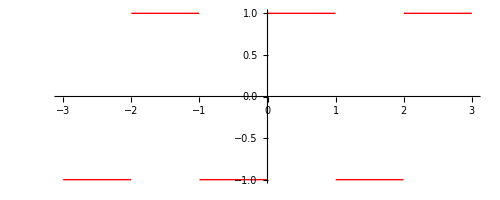

```mathematica
Exact=Plot[squarewave[x],{x,-3,3},AspectRatio->Automatic, PlotStyle->{Red,Thick}]
```

```mathematica
FourierTrigSeries[squarewave[x],x,15,FourierParameters->{0,1/2}]
```

1/(√2)((4 √2 Sin[π x])/π+(4 √2 Sin[3 π x])/(3 π)+(4 √2 Sin[5 π x])/(5 π)+(4 √2 Sin[7 π x])/(7 π)+(4 √2 Sin[9 π x])/(9 π)+(4 √2 Sin[11 π x])/(11 π)+(4 √2 Sin[13 π x])/(13 π)+(4 √2 Sin[15 π x])/(15 π))

```mathematica
Expand[%]
```

(4 Sin[π x])/π+(4 Sin[3 π x])/(3 π)+(4 Sin[5 π x])/(5 π)+(4 Sin[7 π x])/(7 π)+(4 Sin[9 π x])/(9 π)+(4 Sin[11 π x])/(11 π)+(4 Sin[13 π x])/(13 π)+(4 Sin[15 π x])/(15 π)

```mathematica
f[x_,n_]:=∑_(k=0)^n (4Sin[(2k+1)π x])/((2k+1)π)
```

```mathematica
f[x,7]
```

(4 Sin[π x])/π+(4 Sin[3 π x])/(3 π)+(4 Sin[5 π x])/(5 π)+(4 Sin[7 π x])/(7 π)+(4 Sin[9 π x])/(9 π)+(4 Sin[11 π x])/(11 π)+(4 Sin[13 π x])/(13 π)+(4 Sin[15 π x])/(15 π)

```mathematica
Manipulate[Plot[f[x,n],{x,-3,3},AspectRatio->Automatic],{n,5,25,5}]
```

```mathematica
gibbs[x_,n_]:=1-f[x,n]
absolutegibbs[x_,n_]:=Abs[gibbs[x,n]]
```

```mathematica
Manipulate[Plot[absolutegibbs[x,n],{x,0,1},PlotRange->{0,1}],{n,5,25,1}]
```

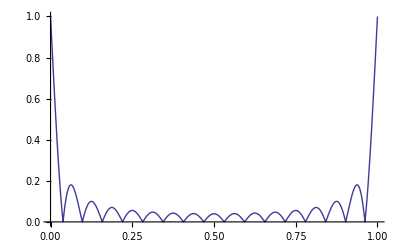

```mathematica
Plot[Abs[gibbs[x,7]],{x,0,1},PlotRange->{0,1}]
```

Problem 5:  Griffiths' "Needle Problem"

```mathematica
gibbsprime[x_,n_]:=D[gibbs[x,n],x]
```

```mathematica
Clear[x]
```

```mathematica
NSolve[{gibbsprime[x,7]==0,Abs[x]==x},x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.0625},{x→0.125},{x→0.1875},{x→0.25},{x→0.3125},{x→0.375},{x→0.4375},{x→0.5},{x→0.5625},{x→0.625},{x→0.6875},{x→0.75},{x→0.8125},{x→0.875},{x→0.9375}}

```mathematica
peaks={x,Abs[gibbs[x,7]]}/.%
```

{{0.0625,0.180284},{0.125,0.099821},{0.1875,0.0702449},{0.25,0.0556522},{0.3125,0.0475143},{0.375,0.0428475},{0.4375,0.0404008},{0.5,0.0396362},{0.5625,0.0404008},{0.625,0.0428475},{0.6875,0.0475143},{0.75,0.0556522},{0.8125,0.0702449},{0.875,0.099821},{0.9375,0.180284}}

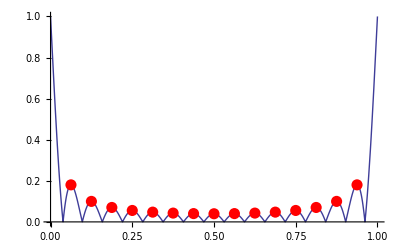

```mathematica
Plot[Abs[gibbs[x,7]],{x,0,1},PlotRange->{0,1},
Epilog->{PointSize[0.02],Red,Map[Point,peaks]}]
```

```mathematica
?Fit
```

Fit[data,funs,vars] finds a least-squares fit to a list of data as a linear combination of the functions funs of variables vars.

```mathematica
Fit[peaks, {1,1/(x(1-x))^(1/2)},x]
```

-0.0950098+0.0658782/(√((1-x) x))

```mathematica
GriffithsAndLi[x_]:=-0.0950098359453018+0.06587823453635137/(√((1-x) x))
```

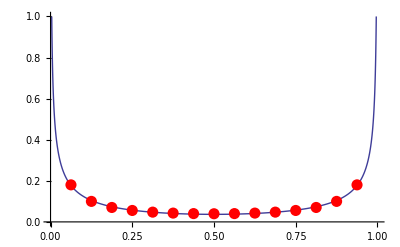

```mathematica
Plot[GriffithsAndLi[x],{x,0,1},PlotRange->{0,1},
Epilog->{PointSize[0.02],Red,Map[Point,peaks]}]
```

```mathematica
Fit[peaks, {1,1/(x(1-x))^(1/3)},x]
```

-0.189381+0.141551/((1-x) x)^(1/3)

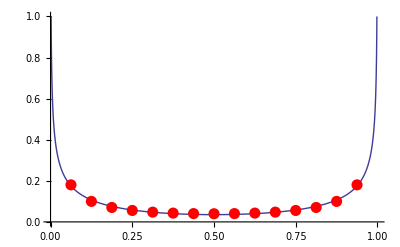

```mathematica
Plot[-0.1893806001173922+0.14155126404863597/((1-x) x)^(1/3),{x,0,1},PlotRange->{0,1},
Epilog->{PointSize[0.02],Red,Map[Point,peaks]}]
```

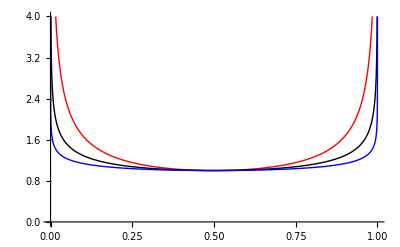

```mathematica
Plot[{(4x(1-x))^(-1/2),(4x(1-x))^(-1/4),(4x(1-x))^(-1/8)},{x,0,1},PlotRange->{0,4},PlotStyle->{Red,Black,Blue}]
```

Problem 5:  Link Creation & Imported Graphic

Hyperlink[uri] represents a hyperlink that jumps to the specified URI when clicked. 
Hyperlink[label,uri] represents a hyperlink to be displayed as label.

```mathematica
Hyperlink["Narcissus","http://en.wikipedia.org/wiki/Narcissus_%28Caravaggio%29"]
```

```mathematica
Import["/Volumes/QUANTUM/Mathematica Labs 2007/Opened Solutions 2007 v.6/Caravaggio's Narcissus.rtfd/300px-Michelangelo_Caravaggio_065.jpg"]
```

-Graphics-